```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Y=Import["LR3_1.txt", "Data"];

L = Y[[1]][[1]];
T=Y[[1]][[2]];
n =Y[[2]][[1]];
m=Y[[2]][[2]];
h=L/(n-1);
tau=T/(m-1);

time = {};data={};
For[i =0 ,i <6,i++,
num =  m /6 * i + 3;
data=Append[data,Table[{h*k,Y[[num]][[k + 1]]},{k,1,n }]];
time= Append[time,Y[[num]][[1]]]];
exactSol[x_,t_] =Sin[Pi * x] * Cos[Pi *t];
```

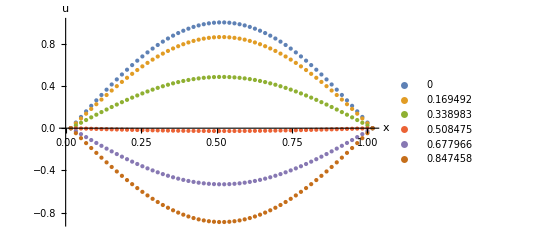

```mathematica
ListPlot[data,AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->time]
```

{0,0.0532222}

{0.169492,0.0458537}

{0.338983,0.0257889}

{0.508475,0.00141687}

{0.677966,0.0282301}

{0.847458,0.0472268}

0.0532222

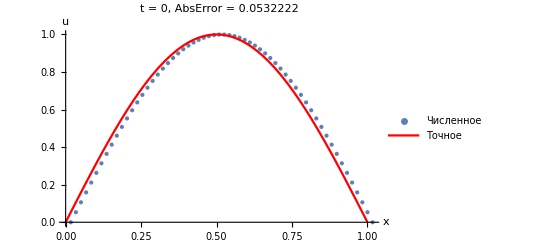

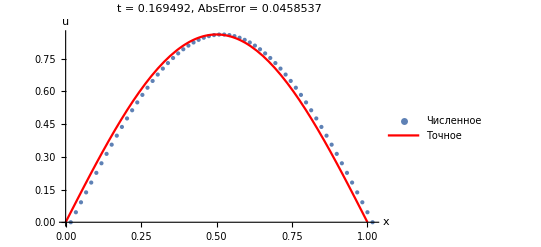

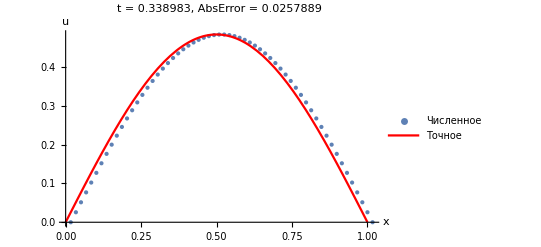

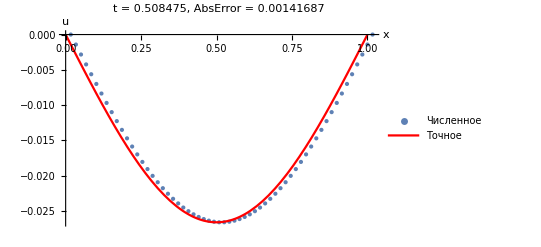

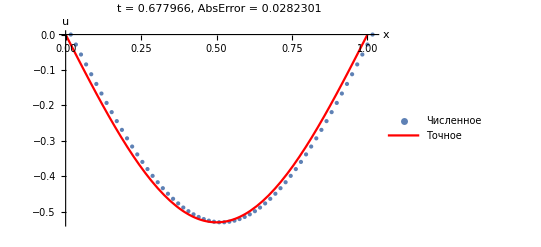

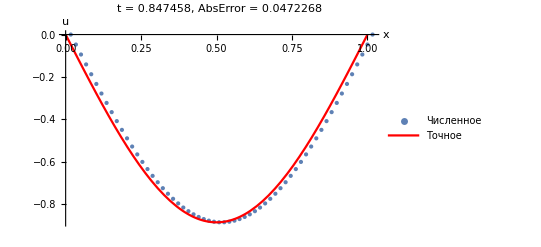

```mathematica
maxError = 0;
For[i =0 ,i <6,i++,
error =Max[Table[{N[Y[[m /6 * i + 3]][[k + 1]] - exactSol[h * k,time[[i+1]]]]},{k,1,n}]];
maxError=Max[{error, maxError}];
{time[[i+1]],error}//Print
];
maxError
For[i =0 ,i <6,i++,
error =Max[Table[{N[Y[[m /6 * i + 3]][[k + 1]] - exactSol[h * k,time[[i+1]]]]},{k,1,n}]];
maxError=Max[{error, maxError}];
Show[ListPlot[data[[i + 1]],AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotLabel->Style[StringJoin[StringJoin["t = ",ToString[time[[i + 1]]]],StringJoin[", AbsError = ",ToString[error]]],Medium],PlotStyle->PointSize[Small],PlotRange->All,PlotLegends->{"Численное"}],
Plot[exactSol[x,time[[i+1]]],{x,0,1},PlotStyle->Red,PlotLegends->{"Точное"},AxesStyle->Thick,LabelStyle->Directive[20]]]//Print
];
```

{0,0.0166642}

{0.169492,0.0112068}

{0.338983,0.00546175}

{0.508475,0.00029342}

{0.677966,0.00603599}

{0.847458,0.0117807}

0.0166642

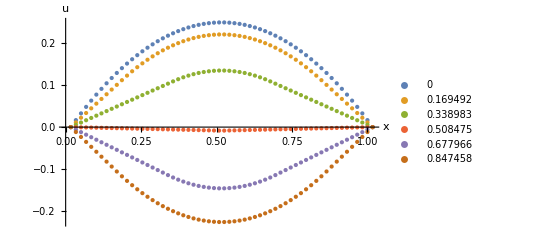

```mathematica
time1 = {};data1={};
Y1=Import["LR3_2.txt", "Data"];
For[i =0 ,i <6,i++,
num =  m /6 * i + 3;
data1=Append[data1,Table[{h*k,Y1[[num]][[k + 1]]},{k,1,n }]];
time1= Append[time1,Y1[[num]][[1]]]];
exactSol1[x_,t_] =8/Pi^3 Sum[1/(2n1+1)^3 Sin[(2n1+1)*Pi*x]Cos[(2n1+1)*Pi*t],{n1,0,k1}];
maxError = 0;
For[i =0 ,i <6,i++,
error =Max[Table[{N[Y1[[m /6 * i + 3]][[k + 1]] - exactSol1[h * k,time1[[i+1]]]]},{k,1,n}]];
maxError=Max[{error, maxError}];
{time1[[i+1]],error}//Print
];
maxError
ListPlot[data1,AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->time1]
```

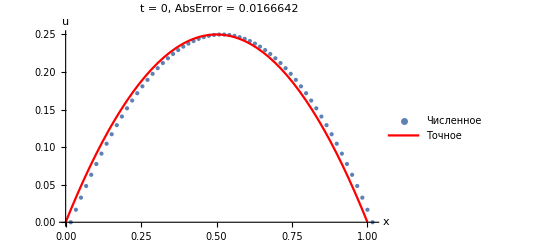

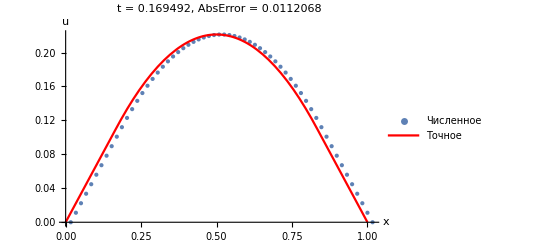

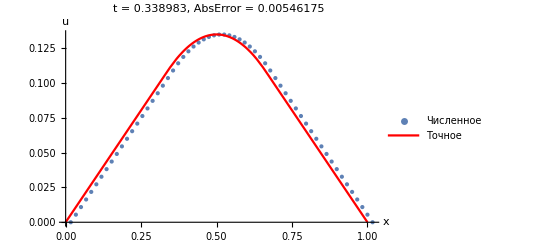

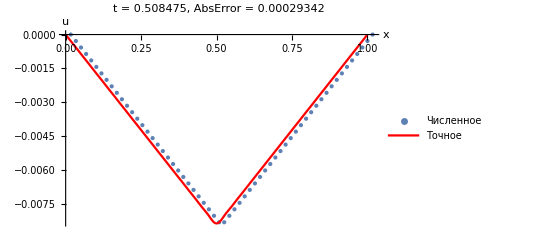

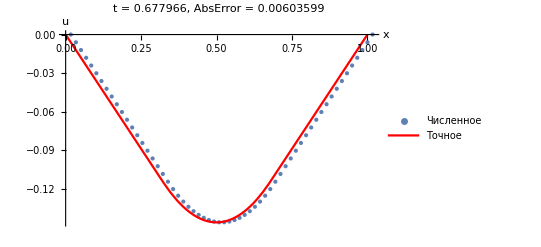

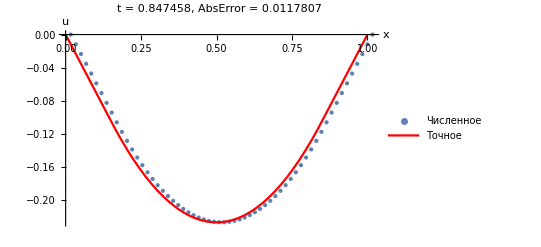

```mathematica
Eps=10^-4;
k1=1/2(Sqrt[2/(Pi^2*Eps)]-1);
Plot[8/Pi^3 Sum[1/(2n1+1)^3 Sin[(2n1+1)*Pi*x]Cos[(2n1+1)*Pi*130*tau],{n1,0,k1}],{x,0,1},PlotStyle->Green,PlotRange->{{0,1},{-1,1}},PlotLegends->{"аналитическое"},AxesLabel->{"x","u"}];
For[i =0 ,i <6,i++,
error =Max[Table[{N[Y1[[m /6 * i + 3]][[k + 1]] - exactSol1[h * k,time1[[i+1]]]]},{k,1,n}]];
maxError=Max[{error, maxError}];
Show[ListPlot[data1[[i + 1]],AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotLabel->Style[StringJoin[StringJoin["t = ",ToString[time1[[i + 1]]]],StringJoin[", AbsError = ",ToString[error]]],Medium],PlotStyle->PointSize[Small],PlotRange->All,PlotLegends->{"Численное"}],
Plot[exactSol1[x,time[[i+1]]],{x,0,1},PlotStyle->Red,PlotLegends->{"Точное"},AxesStyle->Thick,LabelStyle->Directive[20]]]//Print
];
```

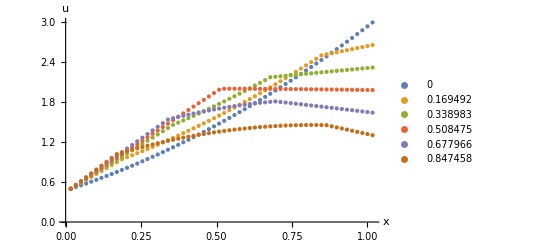

```mathematica
time2 = {};data2={};
Y2=Import["LR3_3.txt", "Data"];
For[i =0 ,i <6,i++,
num =  m /6 * i + 3;
data2=Append[data2,Table[{h*k,Y2[[num]][[k + 1]]},{k,1,n }]];
time2= Append[time2,Y2[[num]][[1]]]];
exactSol2[x_,t_] =8/Pi^3 Sum[1/(2n1+1)^3 Sin[(2n1+1)*Pi*x]Cos[(2n1+1)*Pi*t],{n1,0,k1}];
ListPlot[data2,AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->time2]
```